```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Antonio\Dropbox\4-ResearchProjects\01-Springer-Fractal Tumor Growth\VisibilityGraphs-MMA code-PublicRepository

```mathematica
points =SemanticImport["3C-TB16-meningioma.txt"]
```

13.53 | 61.08 | -3.351
14.09 | 61.08 | -3.351
14.66 | 61.08 | -3.351
12.96 | 61.65 | -3.351
13.53 | 61.65 | -3.351
14.66 | 61.65 | -3.351
15.23 | 61.65 | -3.351
13.53 | 62.21 | -3.351
15.23 | 62.21 | -3.351
15.79 | 62.21 | -3.351
12.96 | 62.78 | -3.351
13.53 | 62.78 | -3.351
15.23 | 62.78 | -3.351
15.79 | 62.78 | -3.351
16.36 | 62.78 | -3.351
12.4 | 63.34 | -3.351
⋮_39112 |  | 
2 levels | 39128rows |  | Dataset[{__List}]

```mathematica
pointsf = Normal@points
```

{{13.5278,61.0792,-3.3509},{14.0942,61.0792,-3.3509},{14.6606,61.0792,-3.3509},39123,{19.1918,80.3368,54.6491},{19.7582,80.3368,54.6491}}
 |  |  |  |

```mathematica
Clear[points]
```

## Volume of tumor’s interface

```mathematica
Show[Graphics3D[{PointSize[Small], Red,Point/@pointsf}]]
```

-Graphics3D-

```mathematica
centerOfMass = {Total [pointsf[[All, 1]]], Total [pointsf[[All, 2]]], Total [pointsf[[All, 3]]]}  / Length[pointsf]
```

{18.1224,75.9421,19.3253}

```mathematica
tal =Reverse@SortBy[Tally[pointsf[[All, 3]]], Last]; tal // Short
```

{{4.1491,655},{17.1491,653},«113»,{54.1491,36},{54.6491,5}}

Z - coordinate with most points

```mathematica
p = First[tal][[1]]
```

4.1491

```mathematica
pointsInBiggestSlice =Select[pointsf,Last[#]==p&]; pointsInBiggestSlice // Short
```

{{23.723,45.7864,4.1491},«653»,{«1»}}

```mathematica
pointsInBiggestSlice // Length
```

655

## Visibility graph for biggest tumor slice (original ordering)

```mathematica
distancesFromCenterBiggestSlice = EuclideanDistance[centerOfMass, #]& /@ pointsInBiggestSlice;
```

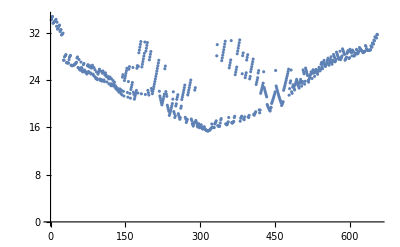
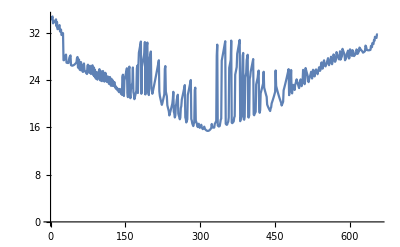

```mathematica
{ListPlot[distancesFromCenterBiggestSlice],ListLinePlot[distancesFromCenterBiggestSlice]}
```

```mathematica
fied[m_,n_,data_]:=If[(Min[#[[m]],#[[n]]]>Max[#[[m+1;;n-1]]])&@data,m<->n]
```

```mathematica
edgesDist=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&  @ distancesFromCenterBiggestSlice;
```

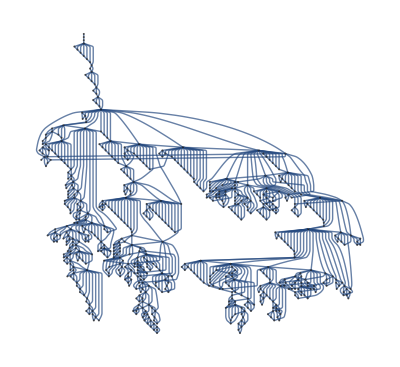

```mathematica
graphBiggestSlice =Graph[edgesDist,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Manipulate[Graph[edgesDist,GraphLayout->embedding], {embedding, {"LayeredDigraphEmbedding", "SpiralEmbedding", "RadialEmbedding","BalloonEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding", "CircularEmbedding", "CircularMultipartiteEmbedding"}}]
```

Degree of vertices in biggest slice

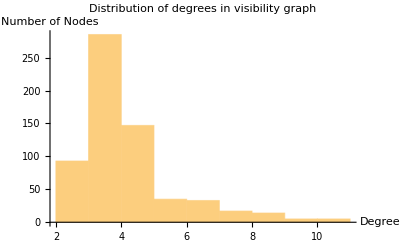

```mathematica
Histogram[VertexDegree[graphBiggestSlice],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## All the tumor slices

```mathematica
distancesFromCenterAllTumor = EuclideanDistance[centerOfMass, #]& /@ pointsf
```

{27.4996,27.4106,27.3331,27.299,27.1976,39118,35.7015,35.3581,35.3786,35.6122,35.6337}
 |  |  |  |

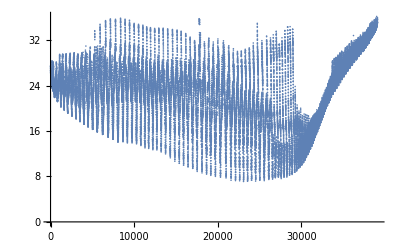

```mathematica
ListPlot[distancesFromCenterAllTumor]
```

```mathematica
distancesFromCenter = EuclideanDistance[centerOfMass, #]& /@ pointsf ;
```

## Visibility grah for the first 2000 points in the interface (original ordering)

```mathematica
dataS= distancesFromCenter[[1;;2000]];
```

```mathematica
edgesS=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&@dataS;
```

```mathematica
gS2000=Graph[#,GraphLayout->"LayeredDigraphEmbedding"]&@edgesS;
gSH2000=HighlightGraph[#,VertexList[#],VertexSize->Thread[VertexList[#]->Rescale[VertexDegree[#]]],ImageSize->{Automatic,500}]&@gS2000
```

-Graphics-

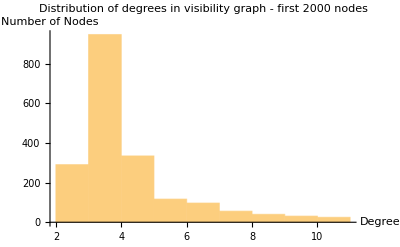

```mathematica
Histogram[VertexDegree[gS2000],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph - first 2000 nodes","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## Attempt of visibility graph for all distances (original ordering)

```mathematica
(*dataS={ distancesFromCenter};
edgesS=Cases[Flatten[ParallelTable[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&/@dataS;
$Aborted
gS=Graph[#,GraphLayout->"LayeredDigraphEmbedding"]&/@edgesS;*)
```

## Ordering of the points according to Travelling Salesman Problem solution

```mathematica
shortestTour =FindShortestTour[pointsf]
```

{34394.2,{1,3,7,88,86,92,338,729,723,1141,724,1143,1142,339,189,89,10,9,14,93,196,347,730,348,210,99,25,26,39073,5,11,90,187,84,179,4,171,166,168,325,83,82,167,693,709,311,310,722,324,346,195,95,91,87,2,81,1}}
 |  |  |  |

Reorder points

```mathematica
tspPoints =pointsf[[Last[shortestTour]]]
```

{{13.5278,61.0792,-3.3509},{14.6606,61.0792,-3.3509},{15.227,61.6456,-3.3509},39124,{13.5278,61.0792,-2.8509},{13.5278,61.0792,-3.3509}}
 |  |  |  |

```mathematica
tspDistances =EuclideanDistance[centerOfMass, #]& /@ tspPoints
```

{27.4996,27.3331,26.9626,26.2427,26.5435,39119,26.195,26.4841,27.4106,27.0887,27.4996}
 |  |  |  |

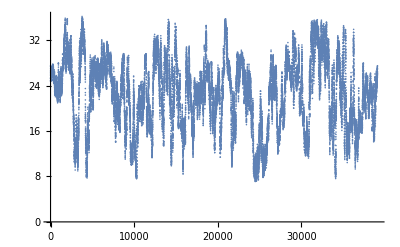

```mathematica
ListPlot[tspDistances]
```

## Visibility graph in slice with most tumor - Travelling Salesman Problem' s solution ordering

```mathematica
tspTourBigSlice =FindShortestTour[pointsInBiggestSlice]; tspTourBigSlice // Short
tspOrderPointsBigSlice =pointsInBiggestSlice[[Last[tspTourBigSlice]]]; tspOrderPointsBigSlice // Short
```

{578.938,{1,5,12,14,22,24,25,«642»,13,3,8,6,7,2,1}}

{{23.723,45.7864,4.1491},«654»,{23.723,45.7864,4.1491}}

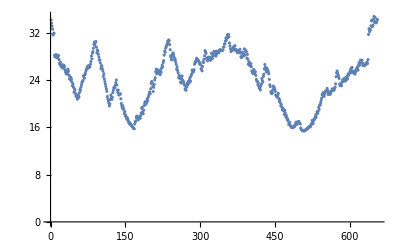
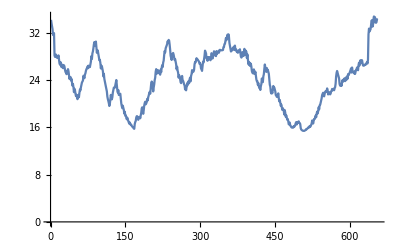

```mathematica
tspDistances = EuclideanDistance[centerOfMass, #]& /@ tspOrderPointsBigSlice; {ListPlot[tspDistances], ListLinePlot[tspDistances]}
```

### Estimation of the Hurst exponent of the “TSP walk”

```mathematica
pars=FindProcessParameters[tspDistances,FractionalBrownianMotionProcess[h]]
```

{h→0.921417}

Correlation plot

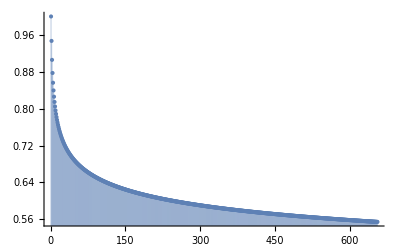

```mathematica
ListPlot[Table[CorrelationFunction[FractionalBrownianMotionProcess[h]/.pars,1,j],{j,Length[pointsInBiggestSlice]}],Filling->Axis,PlotRange->All]
```

```mathematica
edgesDistTSP=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&  @ tspDistances; edgesDistTSP// Short
```

{1<->2,1<->644,1<->645,1<->648,«1297»,652<->655,653<->654,654<->655,655<->656}

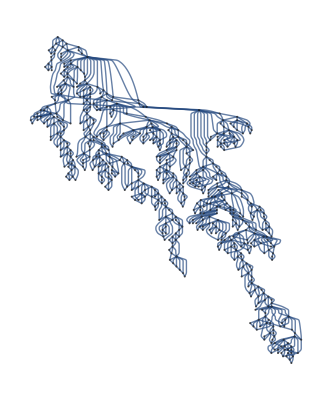

```mathematica
graphBiggestSliceTSP =Graph[edgesDistTSP,GraphLayout->"LayeredDigraphEmbedding"]
```

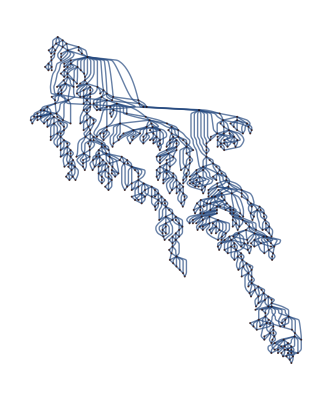

```mathematica
graphBiggestSliceTSPRed =Graph[edgesDistTSP,GraphLayout->"LayeredDigraphEmbedding", VertexStyle-> Red]
```

```mathematica
Manipulate[Graph[edgesDistTSP,GraphLayout->embedding], {embedding, {"SpringEmbedding", "SpiralEmbedding", "RadialEmbedding","BalloonEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding", "CircularEmbedding", "CircularMultipartiteEmbedding"}}]
```

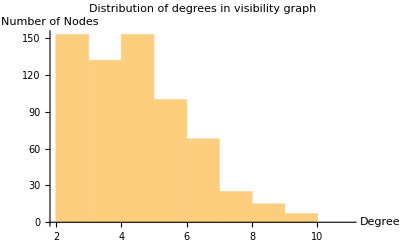

```mathematica
Histogram[VertexDegree[graphBiggestSliceTSP],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## References

"Tumor Growth in the Brain: Complexity and Fractality", Martín-Landrove et al., to be published in Springer’s “The Fractal Geometry of the Brain”

“From Time Series to Complex Networks”, LaCasa et al.
http://www.pnas.org/content/105/13/4972.full

“Visibility graphs - dualism of time series and networks”, Vitaliy Kaurov
http://community.wolfram.com/groups/-/m/t/33771